#### Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documents/Wolfram/Wolfram_scripts/Nano_CSM.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"

fs = 9;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
graphsOpts:= {Mesh-> Full,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> ColorData[3]}
SetOptions[ListLinePlot,graphsOpts];
```

/home/juanathan/Documents/Wolfram/Wolfram_scripts

#### Common Parameters

```mathematica
ang = Range[0,90,1.]*Pi/180.;
lda = {550., 600., 650};

rad = 30.;
cfrac = .3;
(*To recover fresnel*)
ind = Transpose[{1.,1.,1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
(*Au NPs with no size correction*)
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
ind1 = Transpose[{1., 1.} & /@ lda];
ind2 = Transpose[{1., 1.5} & /@ lda];
```

### Fresnel

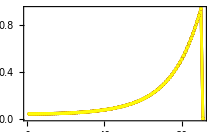
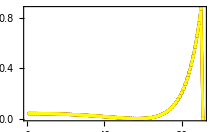
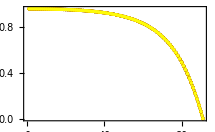
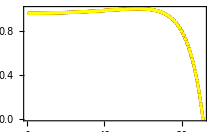

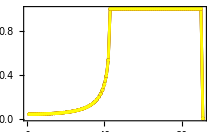
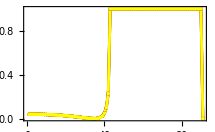
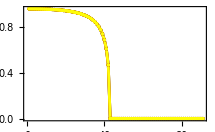
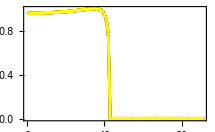

```mathematica
fresnel = Through[{fresnelRs, fresnelRp,fresnelTs,fresnelTp}[ang, toMap/@ind2]]; (*[[rt*pol, ang, lda*)
imp1 = CSMImpedance[ang,#]&/@{ind1, ind1, ind2, ind2};
fresnel= Transpose[fresnel,2<->3];
imp1 = Transpose[imp1, 2<->3];
frext = ListLinePlot[#,PlotRange->All]&/@(imp1*norm2[fresnel])

fresnel = Through[{fresnelRs, fresnelRp,fresnelTs,fresnelTp}[ang, toMap/@ Reverse@ind2]]; (*[[rt*pol, ang, lda*)
imp2 = CSMImpedance[ang,#]&/@{ind1, ind1,  Reverse@ind2,  Reverse@ind2};
fresnel= Transpose[fresnel,2<->3];
imp2 = Transpose[imp2, 2<->3];
frint = ListLinePlot[#,PlotRange->All]&/@(imp2*norm2[fresnel])
```

## Monodisperse (Recovering Fresnel)

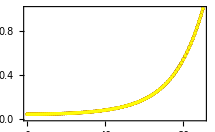
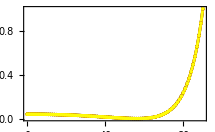

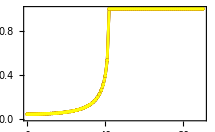
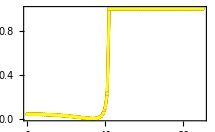

```mathematica
CSM3MediaReflectionExt[ang, ind, lda, rad, cfrac] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSM3MediaReflectionInt[ang, ind, lda, 50., .1];
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %
```

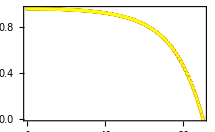
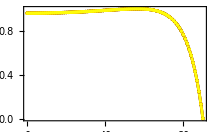

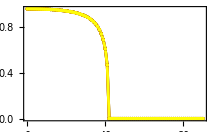
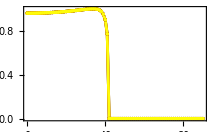

```mathematica
CSM3MediaTransmissionExt[ang, ind, lda, rad, cfrac];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSM3MediaTransmissionInt[ang, ind, lda, 50., .1];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])
```

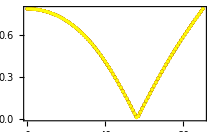
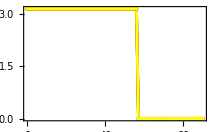

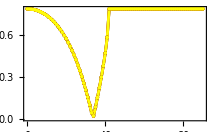
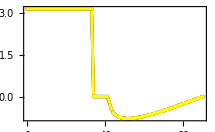

```mathematica
CSM3MediaElipsometryExt[ang, ind, lda, rad, cfrac] ;
ListLinePlot[Transpose@Abs@#, DataRange -> {0, 90}, PlotRange -> All] & /@ %

CSM3MediaElipsometryInt[ang, ind, lda, rad, cfrac];
ListLinePlot[Transpose@#, DataRange -> {0, 90}, PlotRange -> All] & /@ %
```

## Polydisperse (Recovering Fresnel)

0.000104193

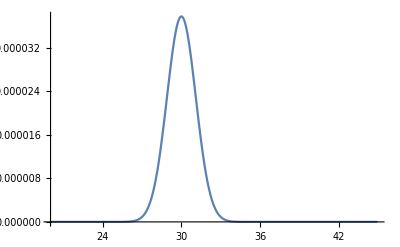

```mathematica
mu  = 30;(*Central value of the Radii Distribution*)
sigma =1.1;(*Standard deviation from Raddii Distribution*)

rhost = cfrac * Exp[-2*Log[sigma]^2]/(Pi * mu^2)(*?? No hay que cambiarlo??*)
sizeDist = rhost * PDF[NormalDistribution[mu,sigma],#]&;
Plot[sizeDist[x],{x,mu*sigma^(-Sqrt[18.]),mu*sigma^(Sqrt[18.])},PlotRange->All]
```

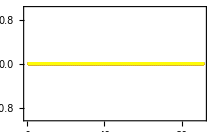
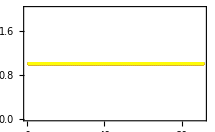

{-Graphics-,-Graphics-}

```mathematica
(*CSMPolyAmplitudeReflectionTransmission = {{rs,ts},{rp,tp}}*)
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM.wls"
data = CSMPolyAmplitudeReflectionTransmission[ang, ind1,lda, cfrac, {mu, sigma, sizeDist}];
ListLinePlot[norm2[#]]&/@Transpose[data[[1]] ,2<->3]
ListLinePlot[norm2[#]]&/@Transpose[data[[2]] ,2<->3]
```

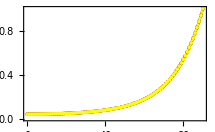
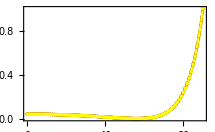

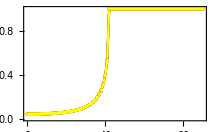
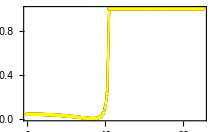

```mathematica
CSMPolyReflectionExt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionInt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %
```

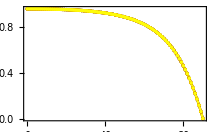
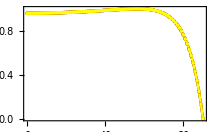

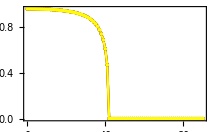
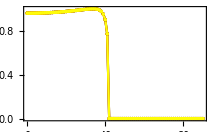

```mathematica
CSMPolyTransmissionExt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSMPolyTransmissionInt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])
```

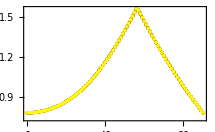
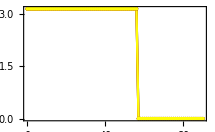

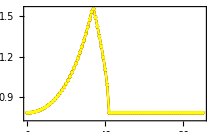
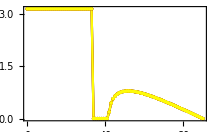

```mathematica
CSMPolyElipsometryExt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyElipsometryInt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %
```

## Mono vs Polydisperse (Gold AuNP)

0.000289425

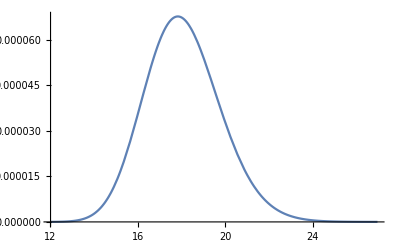

(rhost Exp[-(Log[#1/#2]/(√2. Log[#3]))^2])/(#1 √(2. π) Log[#3])&

```mathematica
mu  = 18;(*Central value of the Radii Distribution*)
sigma =1.1;(*Standard deviation from Raddii Distribution*)

(*Upper and lower integration limits fo the polydispersed case*)
rhost = cfrac * Exp[-2*Log[sigma]^2]/(Pi * mu^2)
sizeDist = rhost * Exp[-(Log[#/#2]/(Sqrt[2.]*Log[#3]))^2] / (#*Sqrt[2.*Pi]*Log[#3])&;
Plot[sizeDist[x,mu,sigma],{x,mu*sigma^(-Sqrt[18.]),mu*sigma^(Sqrt[18.])},PlotRange->All]
sizeDist
```

```mathematica
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
```

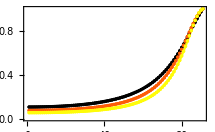
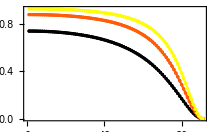

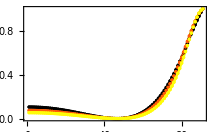
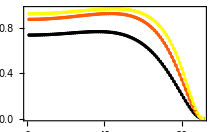

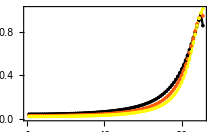
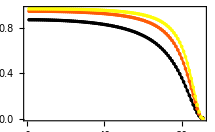

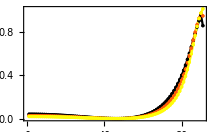
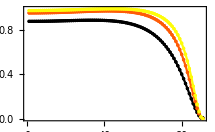

```mathematica
dataMono = CSMAmplitudeReflectionTransmission[ang, indAu[[;;2]],lda, rad,cfrac];
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataMono[[1]] ,2<->3]
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataMono[[2]] ,2<->3]

dataPoly = CSMPolyAmplitudeReflectionTransmission[ang, indAu[[;;2]],lda, cfrac, {mu, sigma, sizeDist}];
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataPoly[[1]] ,2<->3]
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataPoly[[2]] ,2<->3]
```

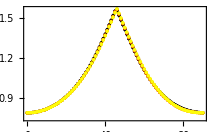
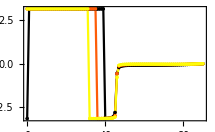

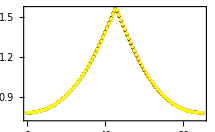
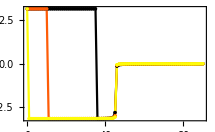

```mathematica
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]&/@ ({ArcTan[Abs[#]],Arg[#]}&@ (Divide@@dataMono[[;;,1]]))
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]&/@ ({ArcTan[Abs[#]],Arg[#]}&@ (Divide@@dataPoly[[;;,1]]))
```

```mathematica
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
```

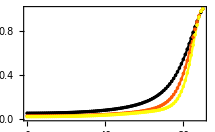
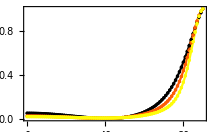

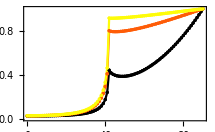
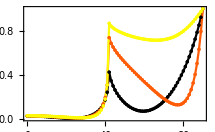

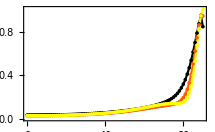
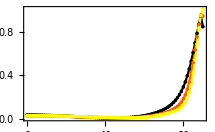

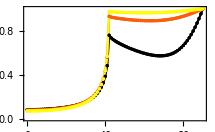
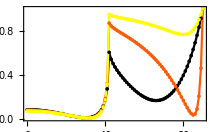

```mathematica
CSM3MediaReflectionExt[ang, indAu, lda, rad, cfrac] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSM3MediaReflectionInt[ang, indAu, lda, rad, cfrac];
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionExt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionInt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %
```

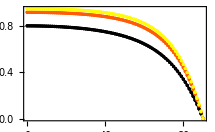
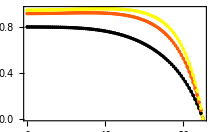

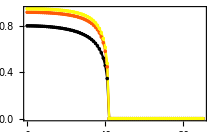
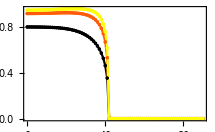

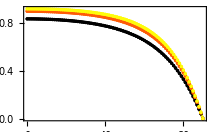
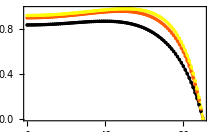

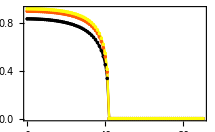
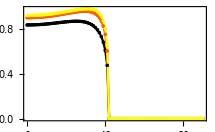

```mathematica
CSM3MediaTransmissionExt[ang, indAu, lda, rad, cfrac];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSM3MediaTransmissionInt[ang, indAu, lda, rad, cfrac];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])

CSMPolyTransmissionExt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSMPolyTransmissionInt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])
```

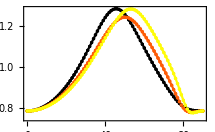
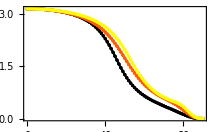

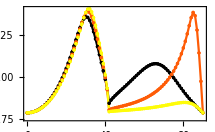
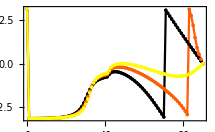

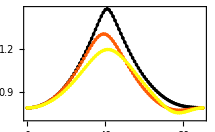
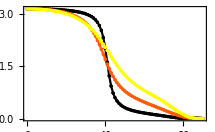

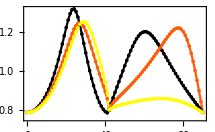
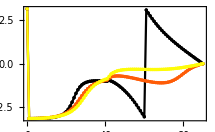

```mathematica
CSMPolyElipsometryExt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyElipsometryInt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSM3MediaElipsometryExt[ang, indAu, lda, rad, cfrac] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSM3MediaElipsometryInt[ang, indAu, lda, rad, cfrac];
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %
```